```mathematica
PointsMA = {{0.10, 0.20},{0.10,0.30},{0.1,0.40},{0.50,0.20},{0.50,0.30},{0.50,0.40},{0.90,0.20},{0.90,0.30},{0.90,0.40}};
```

```mathematica
ValueM120 = {};
For[i=1,i≤ Length[PointsMA],i++,
ValueM120 = Insert[ValueM120,BEMM[PointsMA[[i,1]],PointsMA[[i,2]]],-1]
]
ValueM120
```

{0.550764,0.629848,0.701225,0.652429,0.724614,0.787831,0.924011,0.959372,0.989907}

```mathematica
ValueM60= {};
For[i=1,i≤ Length[PointsMA],i++,
ValueM60 = Insert[ValueM60,BEMM[PointsMA[[i,1]],PointsMA[[i,2]]],-1]
]
ValueM60
```

{0.551203,0.630278,0.701632,0.653107,0.725203,0.788329,0.924841,0.959895,0.990241}

```mathematica
ValueExactMA = {};
For[i=1,i≤ Length[PointsMA],i++,
ValueExactMA= Insert[ValueExactMA,AnalyticSolution2[PointsMA[[i,1]],PointsMA[[i,2]]],-1]
]
ValueExactMA
```

{0.551841,0.630815,0.702062,0.652624,0.724802,0.788019,0.923646,0.959226,0.989775}

```mathematica
PointsMA2 = {{0.10,0.95},{0.10,0.96},{0.10,0.97},{0.0,0.98},{0,0.99}};
```

```mathematica
ValueM1202= {};
For[i=1,i≤ Length[PointsMA2],i++,
ValueM1202 = Insert[ValueM1202,BEMM[PointsMA2[[i,1]],PointsMA2[[i,2]]],-1]
]
ValueM1202
```

{0.983365,0.987142,0.99088,0.992721,0.996405}

```mathematica
ValueExactMA2 = {};
For[i=1,i≤ Length[PointsMA2],i++,
ValueExactMA2= Insert[ValueExactMA2,AnalyticSolution2[PointsMA2[[i,1]],PointsMA2[[i,2]]],-1]
]
ValueExactMA2
```

{0.983369,0.987134,0.99086,0.992695,0.996367}

```mathematica
ValueM1202 - ValueExactMA2
```

{-3.74495×10^-6,7.97227×10^-6,0.0000207005,0.0000256709,0.0000387372}

```mathematica
PointsMA3 = {};
For [i = 1,i ≤ 180,i++,
PointsMA3 = Insert[PointsMA3,N[CoordinateTransform["Polar"-> "Cartesian",{1, i/180 π}],10],-1]
]
```

```mathematica
ValueM1203={};
For[i=1,i≤ Length[PointsMA3],i++,
ValueM1203 = Insert[ValueM1203,BEMM[PointsMA3[[i,1]],PointsMA3[[i,2]]],-1]
]
```

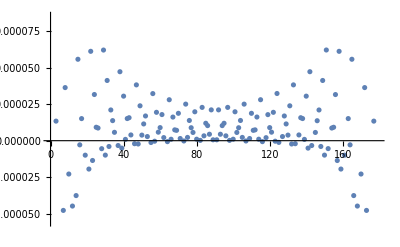

```mathematica
Show[ListPlot[ValueM1203]]
```